```mathematica
sol = NDSolve[{x'[t] == -x[t]+y[t]+Exp[-(1/2)((t-1)/0.1)^2], y'[t] == -y[t]+x[t], x[0] == 1, y[0] == 0},{x,y}, {t,0,5}]
```

{{x→InterpolatingFunction[{{0.,5.}},<>],y→InterpolatingFunction[{{0.,5.}},<>]}}

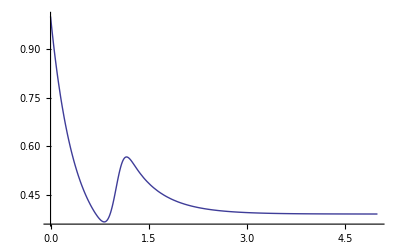

```mathematica
Plot[Evaluate[{ x[t]*x[t]/.sol} ], {t,0,5}, PlotRange->All]
```

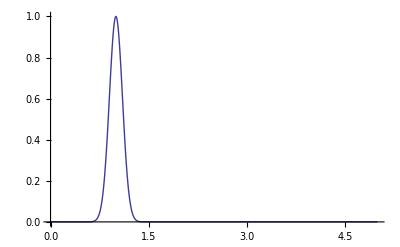

```mathematica
Plot[Exp[-(1/2)((t-1)/0.1)^2],{t,0,5},PlotRange->All]
```